```mathematica
MyHank[x_,t_, d_] = ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2);
QuantPot[x_,t_, d_] = D[MyHank[x,t, d],x,x]/MyHank[x,20, 10]/2;
BohmianForce[x_] = -D[D[MyHank[x,20, 10],x,x]/MyHank[x,20, 10],x];
HydroForce[x_] = -D[MyHank[x,20, 10],x];
```

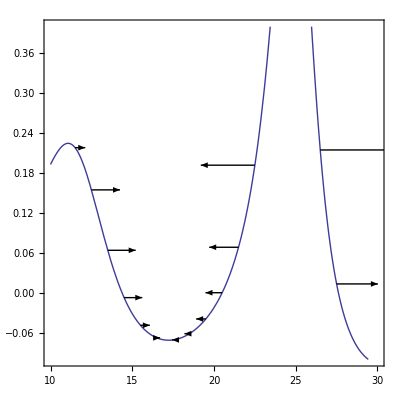

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{x,QuantPot[x,20, 10]},{x+20BohmianForce[x],QuantPot[x,20, 10]}}]}],{x,11.5,28}];
Show[Plot[{QuantPot[x,20, 10]},{x,10,30},PlotRange->{Full,{-0.1,0.4}},Frame->True,Axes->True,FrameTicks->{True,True},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20}],MyForceTestArrows]
```

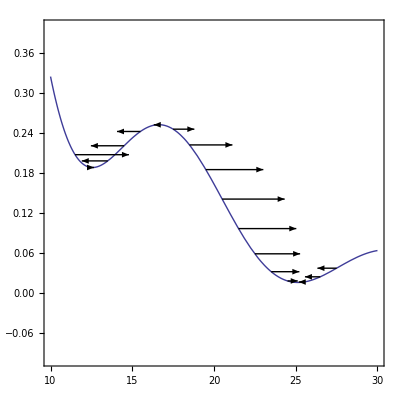

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{x,MyHank[x,20, 10]},{x+84HydroForce[x],MyHank[x,20, 10]}}]}],{x,11.5,28}];
Show[Plot[{MyHank[x,20, 10]},{x,10,30},PlotRange->{Full,{-0.1,0.4}},Frame->True,Axes->True,FrameTicks->{True,True},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20}],MyForceTestArrows]
```

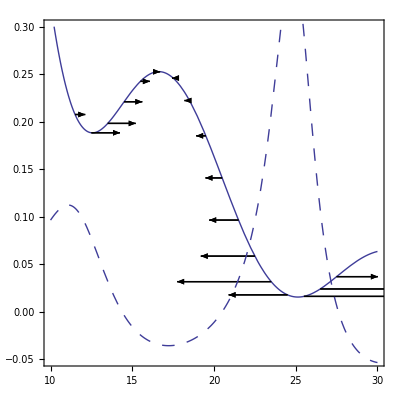

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{x,MyHank[x,20, 10]},{x+20BohmianForce[x],MyHank[x,20, 10]}}]}],{x,11.5,28}];
Show[Plot[{MyHank[x,20, 10]},{x,10,30},PlotRange->{Full,{-0.05,0.3}},Frame->True,Axes->True,FrameTicks->{True,True},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20}],MyForceTestArrows,MyForceTestArrows,Plot[{QuantPot[x,20, 10]},{x,10,30},PlotStyle->{Dashing[Medium]}]]
```

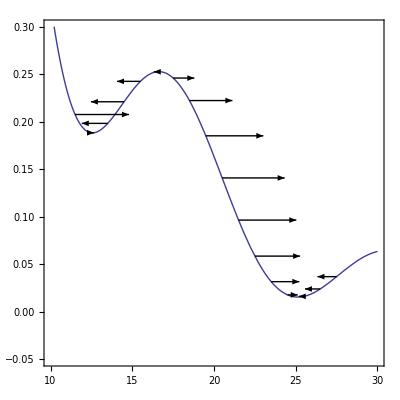

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{x,MyHank[x,20, 10]},{x+84HydroForce[x],MyHank[x,20, 10]}}]}],{x,11.5,28}];
Show[Plot[{MyHank[x,20, 10]},{x,10,30},PlotRange->{Full,{-0.05,0.3}},Frame->True,Axes->True,FrameTicks->{True,True},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20}],MyForceTestArrows]
```